## Uppgift 2

#### Beskrivning

Vinkeln mellan vektorerna a = (2
1
-2), och  b = (3
-2
-1) ska bestämmas.

```mathematica
(*Vektorerna defineras*)
```

```mathematica
a = {2,1,-2};
b = {3,-2,-1};
```

```mathematica
Cross[a,b]
```

{-5,-4,-7}

```mathematica
(* Vinkeln tas fram *)
ang =VectorAngle[a,b]
```

ArcCos[√(2/7)]

```mathematica
ArcCos[√(2/7)] //Degree
```

°[ArcCos[√(2/7)]]

```mathematica
Graphics3D[{Arrow[{{0,0,0},a}],Arrow[{{0,0,0},b}]}]
```

-Graphics3D-

#### Svar

Vinkeln mellan vektorerna är ArcCos[√(2/7)], eller  ca (57,7)^∘

```mathematica
ClearAll["`*"]
```

## Uppgift 4

#### Beskrivning

Beräkna trippelvektor produkten u×(v×w)  för u = (2
3
-2), v = (4
-1
-1),w = (-3
1
2)

(1) Det gäller att trippelskalär produkten u×(v×w)=

```mathematica
u = {2,3,-2} ;
v = {4,-1,-1};
w = {-3,1,2};
```

```mathematica
(*Först beräknas kross produkten för v och w *)
```

```mathematica
vw = Cross[v,w]
(* Därefter tas krossprodukten av vektorn u och (v Cross w) fram*)
result = Cross[u,vw]//MatrixForm
```

{-1,-5,1}

(-7
0
-7)

#### Svar

Trippelvektor produkten är  u × (v × w)=(-7
0
-7)

```mathematica
ClearAll["`*"]
```

## Uppgift 5

#### Beskrivning

Ekvationsystemet Piecewise[{{x-2y, = 3}, {3x+5y, =17}}] ska lösas grafiskt.

```mathematica
system={x-2y== 3,3x+5y == 17};
```

```mathematica
Reduce[system, {x,y}]
```

x==49/11&&y==8/11

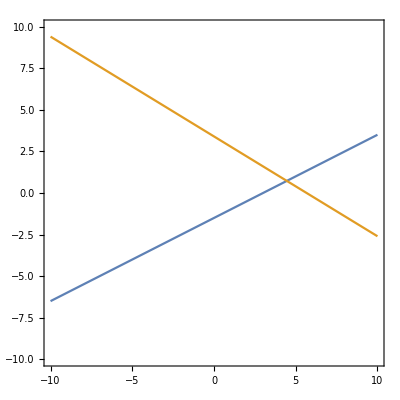

```mathematica
lines=ContourPlot[{x-2y== 3 ,3x+5y == 17},{x,-10,10},{y,-10,10}]
```

#### Svar

Man kan tydligt se att de två linjerna korsar varandra, vilket innebär att det linjära ekvationsystemet har exakt en lösning.

```mathematica
ClearAll["`*"]
```

## Uppgift 7

#### Beskrivning

Följande matriser är givna: A = (3 | 2 | 4
7 | 12 | 0
2 | 5 | 2) ,  B = (5 | 8 | 7
6 | 4 | 9
10 | 1 | 0)  , C= (5 | 22 | 5
5 | 9 | 7
6 | 8 | 2) .
A + B - C , ABC och CBA ska beräknas.

```mathematica
A = {{3,2,4},{7,12,0},{2,5,2}};
B = {{5,8,7},{6,4,9},{10,1,0}};
C1 = {{5,22,5},{5,9,7},{6,8,2}};
MatrixForm[A]
MatrixForm[B]
MatrixForm[C1]
```

(3 | 2 | 4
7 | 12 | 0
2 | 5 | 2)

(5 | 8 | 7
6 | 4 | 9
10 | 1 | 0)

(5 | 22 | 5
5 | 9 | 7
6 | 8 | 2)

(1)  A + B - C beräknas

```mathematica
result1 = A + B - C1
```

{{3,-12,6},{8,7,2},{6,-2,0}}

(2) Skalärprodukt och elementvisa produkter beräknas

```mathematica
(*A B C*)
elementProd= A*B*C1;
MatrixForm[elementProd]
```

(75 | 352 | 140
210 | 432 | 0
120 | 40 | 0)

```mathematica
dotRes1 = A.B.C1 // MatrixForm
```

(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)

```mathematica
(*C B A*)
```

```mathematica
dotRes2 = C1.B.A // MatrixForm
```

(2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)

#### Svar

CBA = (2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)
 ABC =(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)
 A + B - C =(3 | -12 | 6
8 | 7 | 2
6 | -2 | 0)

```mathematica
ClearAll["`*"]
```

## Uppgift 8

#### Beskrivning:

Hitta den radreducerade  trappstegsmatrisen till A = (2 | 4 | 8
4 | 5 | 1
7 | 9 | 3) och ange om den har någon redundans.

#### Lösning:

```mathematica
(*Matrisen A Definieras*)
A = {{2,4,7}, {4,5,9},{8,1,3}};
MatrixForm[A]
```

(2 | 4 | 7
4 | 5 | 9
8 | 1 | 3)

```mathematica
(*Matrisen radreduceras*)
A = RowReduce[A];
MatrixForm[A]
```

(1 | 0 | 1/6
0 | 1 | 5/3
0 | 0 | 0)

#### Svar

Matrisen A har redundans eftersom det den sista kolumnen inte har någon ledande etta.

```mathematica
Clear["Global`*"]
```

## Uppgift 9

#### Beskrivning:

Hitta egenvärden till matrisen (9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

#### Lösning:

(1) Låt M vara en matris

```mathematica
M = {{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}}
```

{{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}}

```mathematica
MatrixForm[M]
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

(2) Egenvärden till A tas fram

```mathematica
Eigenvalues[M]
```

{13,13,-12,-12}

Matrisen har egenvärden 13 och -12

```mathematica
Clear["Global`*"]
```

## Uppgift 10

#### Beskrivning:

Det ska visas att den angivna matrisen är orthogonal

#### Lösning:

(1) kolumn vektorerna v1, v2 ,v3 ,v4 definieras

```mathematica
v1 = {-6,-1,3,6,2,-3,-2,1}
v2={-3,2,6,-3,-1,6,-1,2}
v3 = {6,1,3,6,2,3,2,1}
v4 = {1,-6,-2,-1,3,2,-3,6}
```

{-6,-1,3,6,2,-3,-2,1}

{-3,2,6,-3,-1,6,-1,2}

{6,1,3,6,2,3,2,1}

{1,-6,-2,-1,3,2,-3,6}

(2) Om en kolumnvektor är ortogonal så gäller det att dess Skalärprodukt med resterande kolumnvektorer är noll.

(2.1) v1 testas

```mathematica
v1.v2
v1.v3
v1.v4
```

0

0

0

(2.2) v2 testas

```mathematica
v2.v1
v2.v3
v2.v4
```

0

0

0

(2.3) v3 testas

```mathematica
v3.v1
v3.v2
v3.v4
```

0

0

0

(2.4) v4 testas

```mathematica
v4.v1
v4.v2
v4.v3
```

0

0

0

### Svar:

Eftersom skalärprodukterna allihopa är 0, så matrisens kolumnvektorer ortogonala.

```mathematica
Clear["Global`*"]
```

## Uppgift 13

#### Beskrivning:

Det ska visas att matrisen A = (0.4 | 0.2 | 0.7
0 | 0.6 | 0.1
0.6 | 0.2 | 0.2)  är en reguljär övergångsmatris.

#### Lösning:

(1) Det gäller att en stokatisk övergångs matris A är reguljär om det existerar något n ∈ℕ där alla element i A^n är skilda från noll.

```mathematica
ClearAll["`*"]
```

```mathematica
(* Den stokatiska matrisen A definieras *)
A = {{0.4,0.2,0.7},{0,0.6,0.1},{0.6,0.2,0.2}};
MatrixForm[A]
```

(0.4 | 0.2 | 0.7
0 | 0.6 | 0.1
0.6 | 0.2 | 0.2)

```mathematica
(* Loopen körs för n, n+1 n+2 ... tills matrisen inte har något element som är noll. Loopen skulle dock fortsätta föralltid om den angivna matrisen inte var reguljär *)
```

```mathematica
n = 1;
```

```mathematica
While[!FreeQ[MatrixPower[A,n],0]
Print[Eg = Eigenvalues[MatrixPower[A,n]]]
n++
]
n
```

{1.,0.558258,-0.358258}

2

(1) Den angivna matrisen A är reguljär eftersom det  bevisligen finns något värde för A^n sådant att alla dess element är skillda från noll.

```mathematica
(* Jämnvikts vektor beräknas *)
```

```mathematica
Eigenvalues[A]
```

{1.,0.558258,-0.358258}

```mathematica
Eigenvectors[A]
```

{{-0.771517,-0.154303,-0.617213},{0.473523,-0.81281,0.339287},{0.665163,0.0775016,-0.742665}}

```mathematica
u1 = Eigenvectors[A][[1]]
```

{-0.771517,-0.154303,-0.617213}

```mathematica
s = 1/(u1[[1]] + u1[[2]] + u1[[3]])
```

-0.648074

```mathematica
sc = u1*s ;
MatrixForm[sc]
```

(0.5
0.1
0.4)

```mathematica
A.sc // MatrixForm
```

(0.5
0.1
0.4)

#### Svar

Jämnviktsvektorn är (0.5
0.1
0.4)

```mathematica
Clear["Global`*"]
```

## Uppgift 16

#### Beskrivning:

Avgör om uppsättningen polynom utgör en bas för vektorrummet  P^3

#### Lösing:

```mathematica
v1 = {5,-3,4,2};
v2 = {9,1,8,-6};
v3 = {6,-2,5,0};
v4 = {0,0,1,0};
```

(1) Det är känt att standardbasen för P^3 fås av  B = {1, | t, | t^2, | t^3}.

```mathematica
(*Vektorn A skrivs som en linjär kombination av elementen i basen B*)
```

```mathematica
A = Transpose[{v1,v2,v3,v4}];
```

```mathematica
MatrixForm[A]
```

(5 | 9 | 6 | 0
-3 | 1 | -2 | 0
4 | 8 | 5 | 1
2 | -6 | 0 | 0)

(2) A utgör en bas för vektorrummet om och endast om dess kolumnvektorer är linjärt oberoende.

```mathematica
(*Det undersöks om A är linjärt oberoende genom att ta fram Rank(A), om Rank(A) = Antalet kolumn vektorer så är uppsättningen linjärt oberoende*)
MatrixRank[A]
Det[A]
```

3

0

#### Svar

Eftersom polynomen inte är linjärt oberoende, så utgör den angivna uppsättningen en bas i vektorrummet P^3.

```mathematica
Clear["Global`*"]
```

## Uppgift 18

#### Beskrivning:

Ange diagonalmatrisen D och matriserna P och P^-1  som används för att diagonalisera matrisen A =  (-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

#### Lösning:

```mathematica
ClearAll["`*"]
```

```mathematica
(* Matrisen A defineras *)
A = {{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}};
```

```mathematica
MatrixForm[A]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
(* Matrisens egenvärden samt egen vektorer tas fram *)
```

```mathematica
EigenS = Eigensystem[A]
```

{{5,-2,-2,1},{{2,1,-1,2},{6,-3,0,4},{1,1,1,0},{2,-1,-7,2}}}

```mathematica
(* Diagonalmatrisen D tas fram*)
DiagonalM = DiagonalMatrix[EigenS[[1]]];
```

```mathematica
MatrixForm[DiagonalM]
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)

```mathematica
(* Matrisen P tas fram *)
```

```mathematica
P = Transpose[EigenS[[2]]];
MatrixForm[P]
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

```mathematica
(* Inversen till P tas fram *)
Pinv = Inverse[P];
MatrixForm[Pinv]
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

```mathematica
(* Resultatet dubbelkollas *)
B = P.DiagonalM.Pinv;
MatrixForm[B]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

#### Svar

Diagonal matrisen är :

```mathematica
MatrixForm[DiagonalM]
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)